```mathematica
ClearAll["Global`*"]
```

```mathematica
(*The Data has been taken from the following image. names of the variables are kept the same.*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
ep:={0,0.14,0.24,0.32,0.39,0.44,0.48,0.5,0.53,0.57}(*strains in compression, the -ve sign has been removed*)
```

```mathematica
a:={1.5,1.625,1.8125,2.1875,2.5,2.9375,3.25,3.4275,3.625,2.625}(*right edge of triangle*)
```

```mathematica
b:={1.375,1.4325,1.625,1.84375,2.203125,2.5,2.75, 3.00,3.1875,3.5}(*centre of triangle*)
```

```mathematica
c:={0.05125,0.05125,0.05125,0.05,0.04875,0.0275,0.0275,0.0275,0.05,0.08125}(*height iof the triangle*)
```

```mathematica
Length[a]
```

10

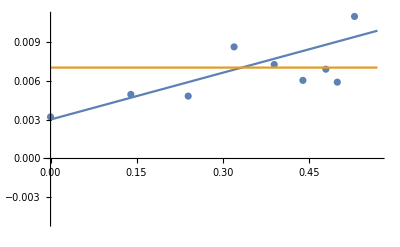

```mathematica
plt11=ListPlot[Transpose@{ep,(a-b)*c/2}];(*right triangle~latent heat/temp vs strain*)
plt12=Plot[{0.003+0.012*(x-0.0),0.007},{x,0,ep[[Length[ep]]]}];
Show[plt11,plt12]
```

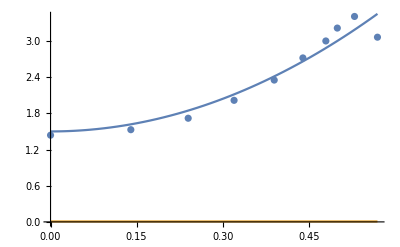

```mathematica
plt21=ListPlot[Transpose@{ep,(a+b)/2}];(*transition temp vs strain*)
plt22=Plot[{1.5+6*(x-0.0)^2,0.007},{x,0,ep[[Length[ep]]]}];
Show[plt21,plt22]
```

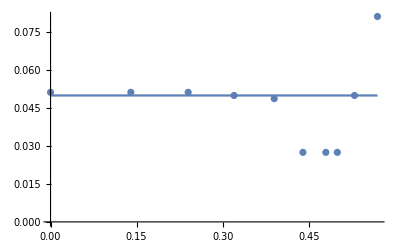

```mathematica
plt31=ListPlot[Transpose@{ep,c}];(*using the jump as (latent heat/\theta_c) vs strain*)
plt32=Plot[{0.05},{x,0,ep[[Length[ep]]]}];
Show[plt31,plt32]
```

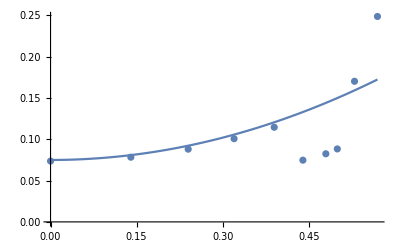

```mathematica
plt41=ListPlot[Transpose@{ep,c*(a+b)/2}];(*\Delta C/\theta\times\theta_c=\Delta C vs strain*)
plt42=Plot[{0.075+0.3*x^2},{x,0,ep[[Length[ep]]]}];
Show[plt41,plt42]
```

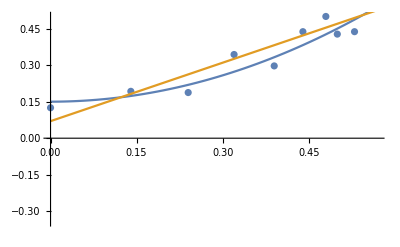

```mathematica
plt51=ListPlot[Transpose@{ep,(a-b)}];(*Transition width vs strain*)
plt52=Plot[{0.15+1.2*(x-0.0)^2,0.07+0.8*x},{x,0,ep[[Length[ep]]]}];
Show[plt51,plt52]
```

```mathematica
Curve Fitting Examples
```

Curve Examples Fitting

```mathematica
(*data={{1980,4716.71636},{1981,4530.36984},{1982,4301.97069},{1983,4335.91656},{1984,4468.26205},{1985,4484.33818},{1986,4487.85587},{1987,4680.83405},{1988,4885.5905},{1989,4948.02116},{1990,5121.17944},{1991,5071.56391},{1992,5174.6706},{1993,5281.38661},{1994,5375.0338},{1995,5436.69799},{1996,5625.04188},{1997,5701.92092},{1998,5749.89306},{1999,5829.51995},{2000,5997.29891},{2001,5899.85548},{2002,5942.42141},{2003,5991.19093},{2004,6105.44411},{2005,6130.55242},{2006,6050.3846},{2007,6127.88822},{2008,5928.25633},{2009,5493.54791},{2010,5700.10834},{2011,5572.58478},{2012,5371.77717},{2013,5522.90837},{2014,5572.10631},{2015,5422.96568},{2016,5306.66246},{2017,5270.74853},{2018,5416.27788}};*)
```

```mathematica
data=Transpose@{ep,c*(a+b)/2}
```

{{0,0.0736719},{0.14,0.0783484},{0.24,0.0880859},{0.32,0.100781},{0.39,0.114639},{0.44,0.0747656},{0.48,0.0825},{0.5,0.0883781},{0.53,0.170313},{0.57,0.248828}}

```mathematica
Length[data]
```

10

```mathematica
(*Method 1 from Stack Exchange*)
```

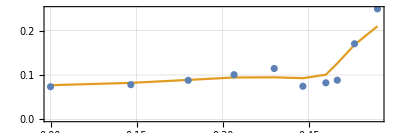

```mathematica
ListPlot[{data,{data[[All,1]],GaussianFilter[data[[All,2]],3]}ᵀ},AspectRatio->1/3,Joined->{False,True},PlotLegends->{"Data","7-Year Trend"},PlotTheme->"Detailed"]
```

```mathematica
(*Method 2 using "Fit"*)
```

```mathematica
parabola=Fit[data,{1,x,x^2},x]
```

0.0920347-0.312247 x+0.823565 x^2

```mathematica
linear=Fit[data,{1,x},x]
```

0.0494776+0.173278 x

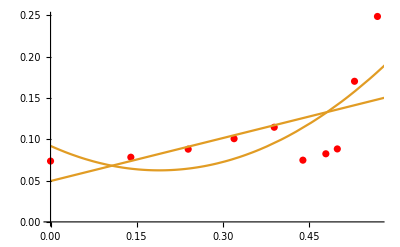

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,0,5}],Plot[{line,linear},{x,0,5}]]
```